```mathematica
mDn=1.86484;
mDc=1.86961;
mDsn=2.00696;
mDsc=2.01026;
mπc=0.139570;
mπn=0.1349766;
```

```mathematica
mDsc-mDn-mπc
mDsn-mDn-mπn
mDsn-mDc-mπc
```

0.00585

0.0071434

-0.00222

```mathematica
λ[x_,y_,z_]:=x^2+y^2+z^2-2*x*y-2*x*z-2*y*z
```

```mathematica
func[z_,m1_:mDn,m2_:mDsc,m3_:mDn,m4_:mDsc,mπ_:mπc]:=NSolve[(m4^2-m3^2-m1^2+m2^2)^2/(4*s)-λ[s,m3^2,m4^2]/(4*s)-λ[s,m1^2,m2^2]/(4*s)+Sqrt[λ[s,m1^2,m2^2]]*Sqrt[λ[s,m3^2,m4^2]]/(2*s)*z-mπ^2==0,s]
```

Part::partw: Part 2 of {{s→16.3016}} does not exist.

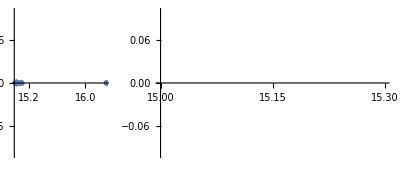

```mathematica
Module[{zv=Subdivide[-1,1,50],cv1,cv2},
cv1=Table[func[z][[1,1,2]],{z,zv}];
cv2=Table[func[z][[2,1,2]],{z,zv}];
GraphicsRow[{ComplexListPlot[cv1,PlotRange->All],ComplexListPlot[cv2,PlotRange->{{15,15.3},{-0.1,0.1}}]}]
]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 2 of {{s→-0.000407253}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

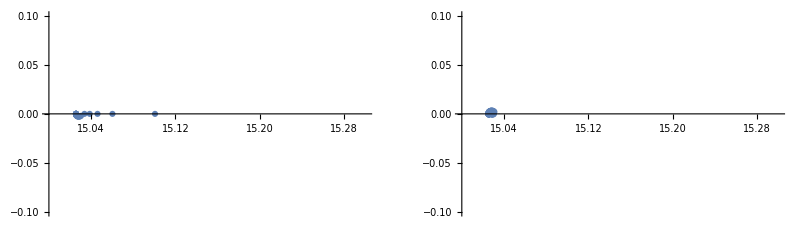

```mathematica
Module[{zv=Subdivide[-1,1,50],cv1,cv2},
cv1=Table[func[z,mDn,mDsc,mDc,mDsn,mπn][[1,1,2]],{z,zv}];
cv2=Table[func[z,mDn,mDsc,mDc,mDsn,mπn][[2,1,2]],{z,zv}];
GraphicsRow[{ComplexListPlot[cv1,PlotRange->{{15,15.3},{-0.1,0.1}}],ComplexListPlot[cv2,PlotRange->{{15,15.3},{-0.1,0.1}}]}]
]
```

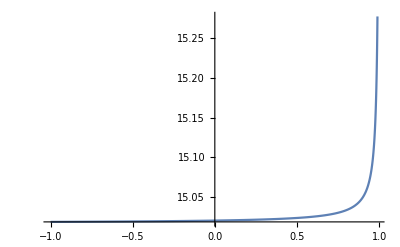

```mathematica
Plot[func[z][[1,1,2]],{z,-1,0.99},PlotRange->All]
```

```mathematica
func[-1][[1,1,2]]-(mDn+mDsc)^2
```

0.00166719

```mathematica
func[1]
```

{{s→16.3016}}

Part::partw: Part 2 of {{s→-4.05618×10^-7}} does not exist.

Part::partw: Part 2 of {{s→-0.000414039}} does not exist.

Part::partw: Part 2 of {{s→-0.000845208}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

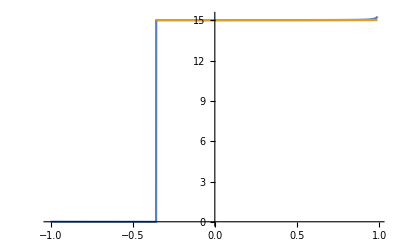

```mathematica
Plot[{Re[func[z,mDn,mDsc,mDc,mDsn,mπn][[1,1,2]]],Re[func[z,mDn,mDsc,mDc,mDsn,mπn][[2,1,2]]]},{z,-1,0.99},PlotRange->All]
```

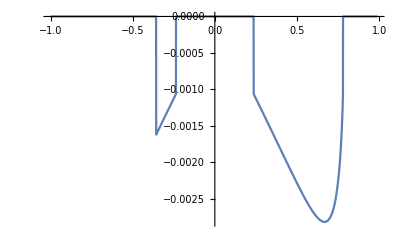

```mathematica
Plot[Im[func[z,mDn,mDsc,mDc,mDsn,mπn][[1,1,2]]],{z,-1,0.99},PlotRange->All]
```

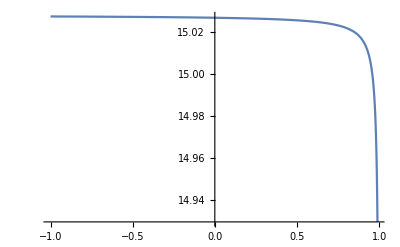

```mathematica
Plot[Re[func[z,mDc,mDsn,mDc,mDsn,mπc][[1,1,2]]],{z,-1,0.99},PlotRange->All]
```

```mathematica
Sqrt[func[1,mDc,mDsn,mDc,mDsn,mπc][[1,1,2]]]-mDc-mDsn
```

-0.0616607

```mathematica
Sqrt[func[-1,mDc,mDsn,mDc,mDsn,mπc][[1,1,2]]]-mDc-mDsn
```

-0.0000792929

```mathematica
expr=((m4^2-m3^2-m1^2+m2^2)^2-λ[s,m1^2,m2^2]-λ[s,m3^2,m4^2]-4*s*mπ^2)^2-4*(s-(m1-m2)^2)*(s-(m1+m2)^2)*(s-(m3-m4)^2)*(s-(m3+m4)^2)*z^2//Expand
```

4 m1^4 m3^4-8 m1^2 m2^2 m3^4+4 m2^4 m3^4-8 m1^4 m3^2 m4^2+16 m1^2 m2^2 m3^2 m4^2-8 m2^4 m3^2 m4^2+4 m1^4 m4^4-8 m1^2 m2^2 m4^4+4 m2^4 m4^4+8 m1^4 m3^2 s-8 m2^4 m3^2 s+8 m1^2 m3^4 s-8 m2^2 m3^4 s-8 m1^4 m4^2 s+8 m2^4 m4^2 s-8 m1^2 m4^4 s+8 m2^2 m4^4 s-16 m1^2 m3^2 mπ^2 s+16 m2^2 m3^2 mπ^2 s+16 m1^2 m4^2 mπ^2 s-16 m2^2 m4^2 mπ^2 s+4 m1^4 s^2+8 m1^2 m2^2 s^2+4 m2^4 s^2+16 m2^2 m3^2 s^2+4 m3^4 s^2+16 m1^2 m4^2 s^2+8 m3^2 m4^2 s^2+4 m4^4 s^2-16 m1^2 mπ^2 s^2-16 m2^2 mπ^2 s^2-16 m3^2 mπ^2 s^2-16 m4^2 mπ^2 s^2+16 mπ^4 s^2-8 m1^2 s^3-8 m2^2 s^3-8 m3^2 s^3-8 m4^2 s^3+16 mπ^2 s^3+4 s^4-4 m1^4 m3^4 z^2+8 m1^2 m2^2 m3^4 z^2-4 m2^4 m3^4 z^2+8 m1^4 m3^2 m4^2 z^2-16 m1^2 m2^2 m3^2 m4^2 z^2+8 m2^4 m3^2 m4^2 z^2-4 m1^4 m4^4 z^2+8 m1^2 m2^2 m4^4 z^2-4 m2^4 m4^4 z^2+8 m1^4 m3^2 s z^2-16 m1^2 m2^2 m3^2 s z^2+8 m2^4 m3^2 s z^2+8 m1^2 m3^4 s z^2+8 m2^2 m3^4 s z^2+8 m1^4 m4^2 s z^2-16 m1^2 m2^2 m4^2 s z^2+8 m2^4 m4^2 s z^2-16 m1^2 m3^2 m4^2 s z^2-16 m2^2 m3^2 m4^2 s z^2+8 m1^2 m4^4 s z^2+8 m2^2 m4^4 s z^2-4 m1^4 s^2 z^2+8 m1^2 m2^2 s^2 z^2-4 m2^4 s^2 z^2-16 m1^2 m3^2 s^2 z^2-16 m2^2 m3^2 s^2 z^2-4 m3^4 s^2 z^2-16 m1^2 m4^2 s^2 z^2-16 m2^2 m4^2 s^2 z^2+8 m3^2 m4^2 s^2 z^2-4 m4^4 s^2 z^2+8 m1^2 s^3 z^2+8 m2^2 s^3 z^2+8 m3^2 s^3 z^2+8 m4^2 s^3 z^2-4 s^4 z^2

```mathematica
CoefficientList
```